```mathematica
<<CustomTicks`
```

```mathematica
tickll=LogTicks[-8,-0.1];
Do[tickll[[i,1]]=10^tickll[[i,1]],{i,1,Length[tickll]}];
tickll;
```

## Our result

```mathematica
mzplist={4,5,10,20,30,40,50,60,75};
(*hllhcpre={0.00039124,0.00026244,(*0.00032177,*)0.00026177,0.00030494,0.00038412,0.00057995,0.00104506,0.00261953}(**6.0 wrong*);*)
hllhcpre={0.0017934283852702538,0.0014596727730310124,0.0016524645426578527,0.001814549760699258,0.00278456495065319,0.006651602786276098,0.016154464478550207,0.05199449543294608,2.25322882404636};
hllhcpreanomalous={0.0006453876905096482,0.0006265903209839063,0.001202686494201666,0.0019634497366490472,0.0035998558933931645,0.009432452022465036,0.021805995561831226,0.07105059160235512,3.201978701780413};
(*run2pre={0.00094856,0.00060939,0.00053095,0.00071368,0.00095795,0.00142996,0.0025633,0.00597184}(**3 wrong*);*)
run2pre={0.005101584531569911,0.0041085089849978804,0.004406372214900768,0.005000095878896492,0.007592657989347046,0.015816214491462952,0.041655345170384335,0.13062954231842722,5.335158963595302};
run2preanomalous={0.0017861084318145876,0.0017352686590079557,0.003126942542743356,0.005361279545397172,0.009605733530545883,0.022506082124984023,0.05584782336291977,0.17783841814406387,6.88958348899121};
hllhcdata=Table[{mzplist[[i]],hllhcpre[[i]]},{i,1,Length[mzplist]}];
hllhcdataanomalous=Table[{mzplist[[i]],hllhcpreanomalous[[i]]},{i,1,Length[mzplist]}];
run2data=Table[{mzplist[[i]],run2pre[[i]]},{i,1,Length[mzplist]}];
run2dataanomalous=Table[{mzplist[[i]],run2preanomalous[[i]]},{i,1,Length[mzplist]}];
```

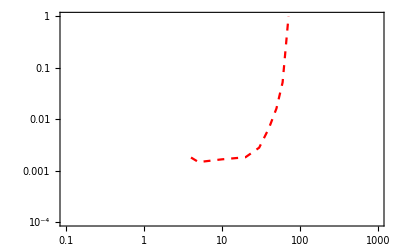

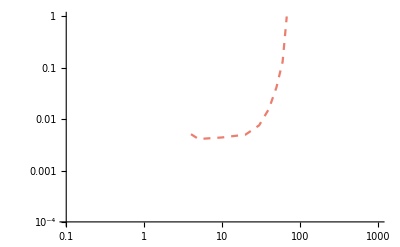

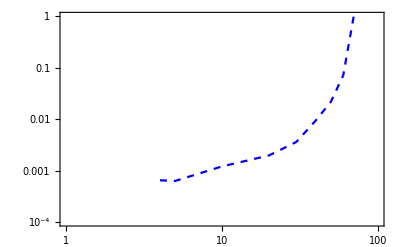

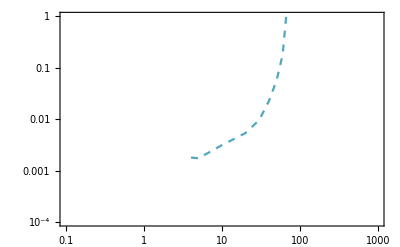

```mathematica
hllhcplot=ListLogLogPlot[hllhcdata,Joined->True,PlotRange->{{0.1,1000},{10^-4,1}},PlotStyle->{Red,Dashed,Thickness[0.004]},Frame->True]
run2plot=ListLogLogPlot[run2data,Joined->True,PlotRange->{{0.1,1000},{10^-4,1}},PlotStyle->{ColorData[24][1],Dashed,Thickness[0.004]}]
hllhcanomalousplot=ListLogLogPlot[hllhcdataanomalous,Joined->True,PlotRange->{{1,100},{10^-4,1}},PlotStyle->{Blue,Dashed,Thickness[0.004]},Frame->True,FrameTicks->{{tickll,Automatic},{Automatic,Automatic}}]
run2anomalousplot=ListLogLogPlot[run2dataanomalous,Joined->True,PlotRange->{{0.1,1000},{10^-4,1}},PlotStyle->{ColorData[24][5],Dashed,Thickness[0.004]},Frame->True]
```

## Data

```mathematica
Babardata=Import["E:\\李沛然\\课程\\物理\\Particle research\\W_lllvl\\plot\\constraint_data\\Babar_data.csv","CSV"];
CMSdata=Import["E:\\李沛然\\课程\\物理\\Particle research\\W_lllvl\\plot\\constraint_data\\CMS_data.csv","CSV"];
ATLASdata=Import["E:\\李沛然\\课程\\物理\\Particle research\\W_lllvl\\plot\\constraint_data\\ATLAS_data.csv","CSV"];
CCFRdata=Import["E:\\李沛然\\课程\\物理\\Particle research\\W_lllvl\\plot\\constraint_data\\CCFR_data.csv","CSV"];
LEPdata=Import["E:\\李沛然\\课程\\物理\\Particle research\\W_lllvl\\plot\\constraint_data\\LEP_data.csv","CSV"];
Bdata=Import["E:\\李沛然\\课程\\物理\\Particle research\\W_lllvl\\plot\\constraint_data\\B_data.csv","CSV"];
```

```mathematica
upsilonlist={9,10,11};
upsilonpre={10^-5,10^-5,10^-5};
upsilondata=Table[{upsilonlist[[i]],upsilonpre[[i]]},{i,1,Length[upsilonlist]}];
```

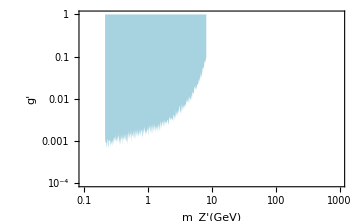

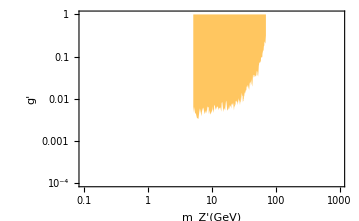

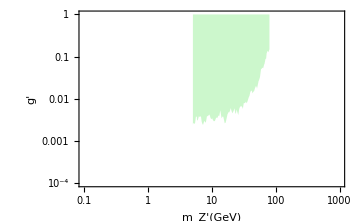

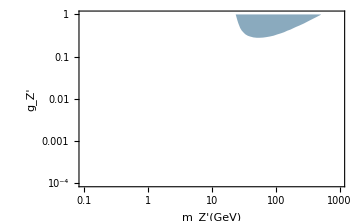

ListLogLogPlot::lpn: upsilondata 不是由数字或者数对组成的列表.

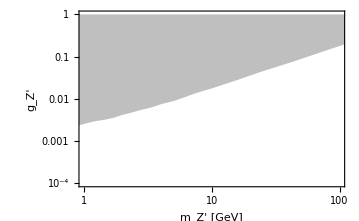

```mathematica
Babarplot=ListLogLogPlot[Babardata,Joined->True,PlotRange->{{0.1,1000},{10^-4,1}},Filling->Top,FillingStyle->Directive[Opacity[0.5],ColorData[24][5]],PlotStyle->{White,Opacity[0]},Frame->True,FrameLabel->{Style["m_Z'(GeV)",Black,13,FontFamily->"Times"],Style["g'",Black,13,FontFamily->"Times"]}(*,FrameTicks->{{yaxis1,Automatic},{xaxis10TeV,Automatic}}*)]
CMSplot=ListLogLogPlot[CMSdata,Joined->True,PlotRange->{{0.1,1000},{10^-4,1}},Filling->Top,FillingStyle->Directive[Opacity[0.8],ColorData[24][2]],PlotStyle->{ColorData[24][3],Opacity[0]},Frame->True,FrameLabel->{Style["m_Z'(GeV)",Black,13,FontFamily->"Times"],Style["g'",Black,13,FontFamily->"Times"]}(*,FrameTicks->{{yaxis1,Automatic},{xaxis10TeV,Automatic}}*)]
ATLASplot=ListLogLogPlot[ATLASdata,Joined->True,PlotRange->{{0.1,1000},{10^-4,1}},Filling->Top,FillingStyle->Directive[Opacity[0.2],Darker[Green,0.15]],PlotStyle->{ColorData[24][3],Opacity[0]},Frame->True,FrameLabel->{Style["m_Z'(GeV)",Black,13,FontFamily->"Times"],Style["g'",Black,13,FontFamily->"Times"]}(*,FrameTicks->{{yaxis1,Automatic},{xaxis10TeV,Automatic}}*)]
LEPplot=ListLogLogPlot[LEPdata,Joined->True,PlotRange->{{0.1,1000},{10^-4,1}},Filling->Top,FillingStyle->Directive[Opacity[0.5],ColorData[24][7]],PlotStyle->{White,Opacity[0]},Frame->True,FrameLabel->{Style["m_Z'(GeV)",Black,30,FontFamily->"Times"],Style["g_Z'",Black,30,FontFamily->"Times"]}(*,FrameTicks->{{yaxis1,Automatic},{xaxis10TeV,Automatic}}*)]
upsilonplot=ListLogLogPlot[upsilondata,Joined->True,PlotRange->{{1,100},{10^-4,1}},Filling->Top,FillingStyle->Directive[Opacity[1],Gray],PlotStyle->{White,Opacity[0]},Frame->True,FrameLabel->{Style["m_Z'(GeV)",Black,30,FontFamily->"Times"],Style["g_Z'",Black,30,FontFamily->"Times"]}(*,FrameTicks->{{yaxis1,Automatic},{xaxis10TeV,Automatic}}*)];
Bplot=ListLogLogPlot[Bdata,Joined->True,PlotRange->{{1,100},{10^-4,1}},Filling->Bottom,FillingStyle->Directive[Opacity[0.2],Darker[Green,0.15]],PlotStyle->{White,Opacity[0]},Frame->True,FrameLabel->{Style["m_Z'(GeV)",Black,30,FontFamily->"Times"],Style["g_Z'",Black,30,FontFamily->"Times"]}(*,FrameTicks->{{yaxis1,Automatic},{xaxis10TeV,Automatic}}*)];
CCFRplot=ListLogLogPlot[CCFRdata,Joined->True,PlotRange->{{1,100},{10^-4,1}},Filling->Top,FillingStyle->Directive[Opacity[0.5],Gray],PlotStyle->{White,Opacity[0]},Frame->True,FrameTicks->{{tickll,Automatic},{Automatic,Automatic}},FrameLabel->{Style["m_Z' [GeV]",Black,50,FontFamily->"Times"],Style["g_Z'",Black,50,FontFamily->"Times"]}(*,FrameTicks->{{yaxis1,Automatic},{xaxis10TeV,Automatic}}*)]
```

## Sum plot

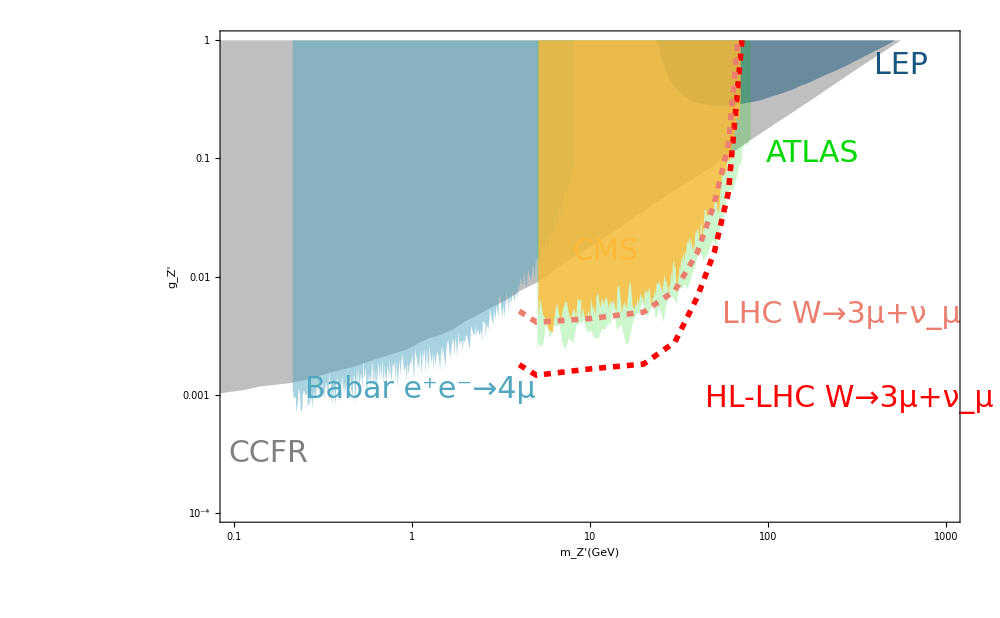

E:\李沛然\课程\物理\Particle research\W_lllvl\plot\sensitivity_final_plot\Zp_sensitivity_total.pdf

```mathematica
sumplot=Show[CCFRplot,LEPplot,Babarplot,ATLASplot,CMSplot,hllhcplot,run2plot(*,hllhcanomalousplot*),FrameTicksStyle->Directive[Black,30,FontFamily->"Times"],Epilog->{Text[Style["CCFR",Gray,30,FontFamily->"Times"],Scaled[{0.065,0.14}],Center,{1,0}],Text[Style["LEP",ColorData[24][7],30,FontFamily->"Times"],Scaled[{0.92,0.93}],Center,{1,0}],Text[Style["Babar e^+e^-→4μ",ColorData[24][5],30,FontFamily->"Times"],Scaled[{0.27,0.27}],Center,{1,0}],Text[Style["CMS",ColorData[24][2],30,FontFamily->"Times"],Scaled[{0.52,0.55}],Center,{1,0}],Text[Style["ATLAS",Darker[Green,0.15],30,FontFamily->"Times"],Scaled[{0.80,0.75}],Center,{1,0}],Text[Style["LHC W→3μ+ν_μ",ColorData[24][1],30,FontFamily->"Times"],Scaled[{0.84,0.42}],Center,{1,0}],(*Text[Style["HL-LHC Anomalous W→3μ+ν_μ",Black,30,FontFamily->"Times"],Scaled[{0.60,0.06}],Center,{1,0}],*)Text[Style["HL-LHC W→3μ+ν_μ",Red,30,FontFamily->"Times"],Scaled[{0.85,0.25}],Center,{1,0}]},ImageSize->1000]
Export["E:\\李沛然\\课程\\物理\\Particle research\\W_lllvl\\plot\\sensitivity_final_plot\\Zp_sensitivity_total.pdf",sumplot,ImageResolution->1000]
```

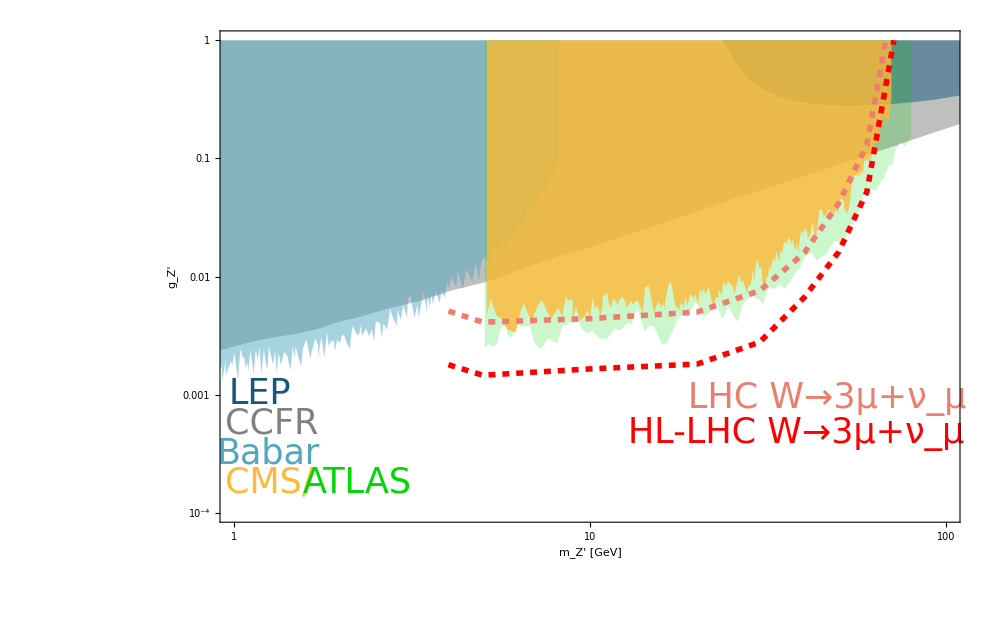

E:\李沛然\课程\物理\Particle research\W_lllvl\plot\sensitivity_final_plot\Zp_sensitivity.pdf

```mathematica
sumplot=Show[CCFRplot(*,upsilonplot*)(*,Bplot*),LEPplot,Babarplot,ATLASplot,CMSplot,hllhcplot,run2plot(*,run2anomalousplot*),FrameTicksStyle->Directive[Black,40,FontFamily->"Times"],Epilog->{Text[Style["CCFR",Gray,35,FontFamily->"Times"],Scaled[{0.07,0.2}],Center,{1,0}],Text[Style["LEP",ColorData[24][7],35,FontFamily->"Times"],Scaled[{0.054,0.26}],Center,{1,0}],Text[Style["Babar",ColorData[24][5],35,FontFamily->"Times"],Scaled[{0.0658,0.14}],Center,{1,0}],Text[Style["CMS/",ColorData[24][2],35,FontFamily->"Times"],Scaled[{0.067,0.08}],Center,{1,0}],Text[Style["ATLAS",Darker[Green,0.15],35,FontFamily->"Times"],Scaled[{0.185,0.08}],Center,{1,0}],(*Text[Style["B_s mixing",Darker[Green,0.15],28,FontFamily->"Times"],Scaled[{0.08,0.032}],Center,{1,0}],*)Text[Style["LHC W→3μ+ν_μ",ColorData[24][1],35,FontFamily->"Times"],Scaled[{0.82,0.25}],Center,{1,0}],Text[Style["HL-LHC W→3μ+ν_μ",Red,35,FontFamily->"Times"],Scaled[{0.778,0.18}],Center,{1,0}](*,Text[Style["LHC Anomalous W→3μ+ν_μ",Black,19,FontFamily->"Times"],Scaled[{0.86,0.14}],Center,{1,0}]*)},ImageSize->1000]
Export["E:\\李沛然\\课程\\物理\\Particle research\\W_lllvl\\plot\\sensitivity_final_plot\\Zp_sensitivity.pdf",sumplot,ImageResolution->1000]
```

```mathematica
hllhcplot=ListLogLogPlot[hllhcdata,Joined->True,PlotRange->{{0.1,1000},{10^-4,1}},PlotStyle->{Red,(*Dashed,*)Thickness[0.004]},Frame->True];
run2plot=ListLogLogPlot[run2data,Joined->True,PlotRange->{{0.1,1000},{10^-4,1}},PlotStyle->{ColorData[24][1],(*Dashed,*)Thickness[0.004]}];
hllhcanomalousplot=ListLogLogPlot[hllhcdataanomalous,Joined->True,PlotRange->{{1,100},{10^-4,1}},PlotStyle->{Blue,Dashed,Thickness[0.004]},Frame->True,FrameTicks->{{tickll,Automatic},{Automatic,Automatic}},FrameLabel->{Style["m_Z' [GeV]",Black,50,FontFamily->"Times"],Style["g_Z'",Black,50,FontFamily->"Times"]}];
run2anomalousplot=ListLogLogPlot[run2dataanomalous,Joined->True,PlotRange->{{0.1,1000},{10^-4,1}},PlotStyle->{ColorData[24][5],Dashed,Thickness[0.004]},Frame->True];
```

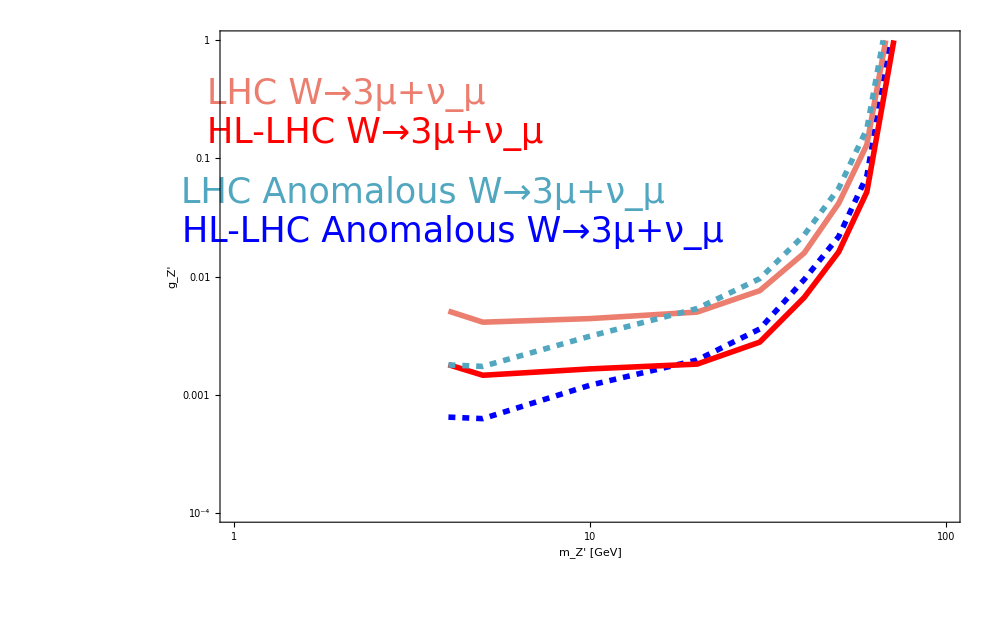

```mathematica
sumplot=Show[hllhcanomalousplot,hllhcplot,run2plot,run2anomalousplot,FrameTicksStyle->Directive[Black,40,FontFamily->"Times"],Epilog->{Text[Style["LHC W→3μ+ν_μ",ColorData[24][1],35,FontFamily->"Times"],Scaled[{0.17,0.87}]],Text[Style["HL-LHC W→3μ+ν_μ",Red,35,FontFamily->"Times"],Scaled[{0.21,0.79}]],Text[Style["LHC Anomalous W→3μ+ν_μ",ColorData[24][5],35,FontFamily->"Times"],Scaled[{0.274,0.67}]],Text[Style["HL-LHC Anomalous W→3μ+ν_μ",Blue,35,FontFamily->"Times"],Scaled[{0.314,0.59}]]},ImageSize->1000]
```